## transcripts init

```mathematica
firstBoardChar[s_String]:=StringMatchQ[StringTake[s,1],"/"|"|"|"\\"|"Y"|"J"|"K"]
```

```mathematica
readBoardsFromTranscript[f_]:=(
Reap[
id=StringDrop[StringDrop[f,11],-4];
Pint[id];
Catch[
While[True,
r=Read[f,String];
Which[
r===EndOfFile,Break[],
StringMatchQ[r,"generating partition #"~~__],(
p=StringCases[r,"generating partition #"~~p__:>p][[1]];
Pint["partition "<>p];
r=Read[f,String];
Which[
StringMatchQ[r,"idhash "~~__~~"hardest is "~~(NumberString)~~__],(
moves=StringCases[r,"idhash "~~__~~"hardest is "~~m:NumberString~~__:>m][[1]];
board=Read[f,{String,String,String,String,String,String,String,String}];
If[And@@(firstBoardChar/@board),Sow[{{"id"->id,"partition"->p,"moves"->moves},board}],Throw[{"not a board",board},1]]
),
StringMatchQ[r,"idhash "~~__~~"hardest is null"~~__],Null,
True,Throw[{"1",r},1]
]
)
]
]
,
1
,
Print["bad",#]&
];
Close[f];
Null
][[2,1]]
)
```

```mathematica
generateDatFileNamesAndContents[transcript_]:=
(
boards=readBoardsFromTranscript[transcript];
(
rules=#[[1]];
data=#[[2]];
file="gen-"<>("id"/.rules)<>"-"<>("partition"/.rules)<>".dat";
{file,"moves: "<>("moves"/.rules)<>"\n"<>StringJoin[((ToString[#]<>"\n")&/@data)]}
)&/@boards
)
```

```mathematica
rotate[m_]:=Reverse/@Transpose[m]
```

```mathematica
empty={
{"/","-","-","-","-","-","-","\\"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"|"," "," "," "," "," "," ","|"},
{"\\","-","-","-","-","-","-","/"}};
```

```mathematica
funcs={#&,rotate[#]&,rotate[rotate[#]]&,rotate[rotate[rotate[#]]]&,Transpose[#]&,Transpose[rotate[#]]&,Transpose[rotate[rotate[#]]]&,Transpose[rotate[rotate[rotate[#]]]]&};
```

```mathematica
applyTransform[level_,trans_]:=(
data=StringReplace[#,"/"|"\\"|"-"|"|"->" "]&/@Characters/@StringCases[StringReplace[level[[2]],first:Shortest[__~~"\n"]~~rest__:>rest],Shortest[a__~~"\n"]:>a];
data2=funcs[[trans]][data];
For[i=1,i≤8,i++,For[j=1,j≤8,j++,If[data2[[i,j]]==" ",data2[[i,j]]=empty[[i,j]]]]];
{level[[1]],StringReplace[level[[2]],first:Shortest[__~~"\n"]~~rest__:>first]<>StringJoin[Append[#,"\n"]&/@data2]}
)
```

## data

```mathematica
counts={#,Flatten[StringCases[ReadList[#,String],"hardest is "~~Shortest[a__]~~" moves":>ToExpression[a]]]}&/@transcriptFileNames;
```

```mathematica
Sort[Flatten[counts[[All,2]]]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,«50964»,62,62,62,62,62,62,62,62,63,63,63,63,63,63,63,63,63,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,69,69,69,70,70,70,71,71,71,71,71,71,71,71,71,71,72,72,73,73,74,74,74,74,74,74,74,74,75,75,76,76,76,76,76,76,76,77,77,77,77,78,78,78,78,81,81,82,82,82,84,85,85,87,87,88,89,89,90,99}

```mathematica
Total[Length[#[[2]]]&/@counts]
```

51234

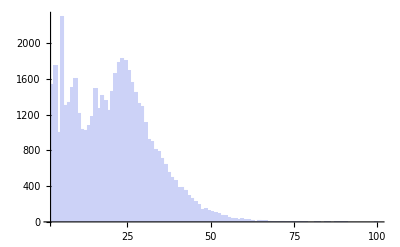

```mathematica
Histogram[Flatten[counts[[All,2]]]]
```

## read transcripts and filter levels

```mathematica
SetDirectory["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\transcripts\\"];
```

```mathematica
transcriptFileNames=FileNames["transcript-*.txt",""];
```

```mathematica
tmp1=generateDatFileNamesAndContents[#]&/@transcriptFileNames;
```

```mathematica
tmp2=Flatten[tmp1,1];
```

```mathematica
tmp3=SortBy[tmp2,StringReplace[#[[2]],"moves: "~~m:NumberString~~__:>ToExpression[m]]&];
```

```mathematica
Length[tmp3]
```

51234

only use required moves of at least 10:

```mathematica
tmp4=Select[tmp3,ToExpression[StringReplace[#[[2]],"moves: "~~m:NumberString~~__:>m]]≥10&];
```

```mathematica
Length[tmp4]
```

38892

and all boards have to have HammingDistance of at least 8 (counting all car letters as equals):

```mathematica
Dynamic[{Length[tmp5],Length[tmp6]}]
```

```mathematica
tmp5=tmp4;
tmp6={};
{Length[tmp5],Length[tmp6]}
While[True,
If[tmp5=={},Break[]];
t=tmp5[[1]];
AppendTo[tmp6,t];
tt=StringReplace[t[[2]],RegularExpression["[ABCDEFG]"]->"A"];
tmp5=Select[tmp5,HammingDistance[tt,StringReplace[#[[2]],RegularExpression["[ABCDEFG]"]->"A"]]>8&];
];
{Length[tmp5],Length[tmp6]}
```

{38892,0}

{0,2396}

apply random transformations to make them look different

```mathematica
SeedRandom[1]
```

```mathematica
tmp7=applyTransform[#,RandomInteger[{1,8}]]&/@tmp6;
```

filter out boards with useless roads or cars

```mathematica
Dynamic[{Length[tmp8],Length[tmp9],t}]
```

```mathematica
tmp8=tmp7;
tmp9={};
While[True,
If[tmp8=={},Break[]];
t=tmp8[[1]];
board=StringReplace[t[[2]],first:Shortest[__~~"\n"]~~rest__:>rest];
res=try[board];
If[res,AppendTo[tmp9,t]];
tmp8=Rest[tmp8];
]
```

```mathematica
tmp9[[1]]
```

{gen-0-4-3-1.dat,moves: 10
/---J--\
|  CCCR|
|     R|
|   BBB|
|      |
|      |
|DDDAAAJ
\-----Y/
}

```mathematica
counts=StringCases[#[[2]],"moves: "~~n:NumberString:>ToExpression[n]][[1]]&/@tmp9;
```

```mathematica
counts=Sort[counts];
```

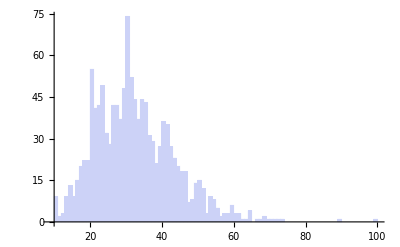

```mathematica
Histogram[counts,{1}]
```

set limit on number of levels with a given number of moves

```mathematica
rules={};
tmp10={};
For[i=1,i≤Length[tmp9],i++,
b=tmp9[[i]];
moves=StringCases[b[[2]],"moves: "~~n:NumberString:>ToExpression[n]][[1]];
If[MemberQ[rules[[All,1]],moves],
already=moves/.rules;
If[already <13,
rules=DeleteCases[rules,moves->_]~Join~{moves->already+1};
AppendTo[tmp10,b];
,
Null
]
,
rules=rules~Join~{moves->1};
AppendTo[tmp10,b];
]
]
```

```mathematica
Length[tmp10]
```

563

```mathematica
counts=StringCases[#[[2]],"moves: "~~n:NumberString:>ToExpression[n]][[1]]&/@tmp10;
```

```mathematica
counts=Sort[counts];
```

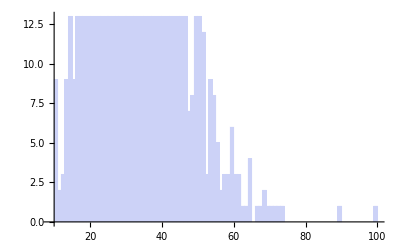

```mathematica
Histogram[counts,{1}]
```

```mathematica
final=tmp10;
```

## episode 1

```mathematica
g=final[[1;;-1;;10]];
```

```mathematica
Length[g]
```

57

```mathematica
g[[-1]]
```

{gen-6-1-5-351.dat,moves: 73
/--Y---\
|RA    |
|RA BBB|
|   C  |
|DD C  |
| GFFE |
J G  E K
\J-K---/
}

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\episode1.zip",g[[All,2]]~Join~{Length[g]},{"ZIP",({#,"Text"}&/@g[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{0.95269,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\episode1.zip}

## episode 2

```mathematica
h=DeleteCases[final,Alternatives@@g];
```

```mathematica
Length[h]
```

506

```mathematica
h[[-2]]
```

{gen-4-3-4-1142.dat,moves: 89
/-Y----\
|  CEE |
J  CF  |
|AACF  |
|BBBF  |
| RDD G|
| R   G|
\--J---/
}

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\episode2.zip",h[[All,2]]~Join~{Length[h]},{"ZIP",({#,"Text"}&/@h[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{5.79622,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\episode2.zip}

## generate tutorial zip file

```mathematica
SetDirectory["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\Bypass\\src\\main\\dat\\tutorial\\"];
```

```mathematica
tutorialFileNames=FileNames["tut-*.dat",""];
```

```mathematica
d={#,Import[#,"Text"]}&/@tutorialFileNames;
```

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\tutorial.zip",d[[All,2]]~Join~{Length[d]},{"ZIP",({#,"Text"}&/@d[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{0.1371,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\tutorial.zip}